## Áreas bajo la curva

a)

4/3

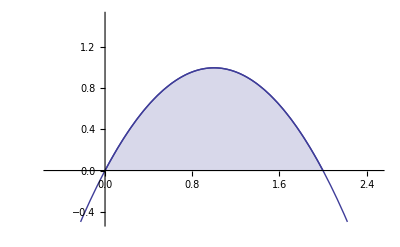

```mathematica
"a)"
f[x_]:=2x-x^2
∫_0^2 f[x]ⅆx
p1:=Plot[f[x],{x,-0.5,2.5},PlotRange->{-0.5,1.5}]
p2:=Plot[f[x],{x,0,2},Filling->Bottom]
Show[p1,p2]
```

b)

32/3

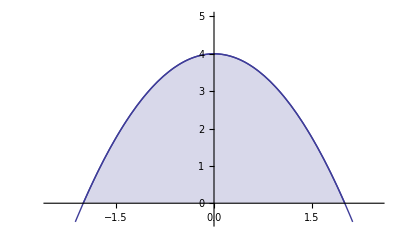

```mathematica
"b)"
f[x_]:=4-x^2
∫_-2^2 f[x]ⅆx
p1:=Plot[f[x],{x,-2.5,2.5},PlotRange->{-0.5,5}]
p2:=Plot[f[x],{x,-2,2},Filling->Bottom]
Show[p1,p2]
```

c)

0.499938

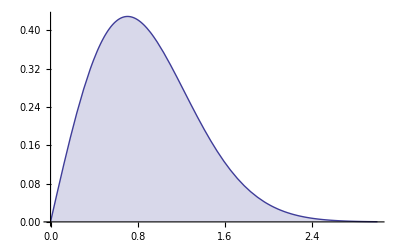

```mathematica
"c)"
f[x_]:=x ⅇ^(-x^2)
N[∫_0^3 f[x]ⅆx]
Plot[f[x],{x,0,3},Filling->Bottom]
```

## Áreas entre curvas

```mathematica
"a)"
f[x_]:=4-x^2
g[x_]:=x^2
Solve[f[x]==g[x],x]
```

a)

{{x→-√2},{x→√2}}

7.54247

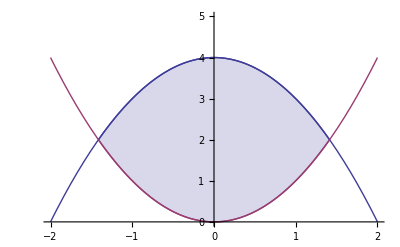

```mathematica
N[∫_(-√2)^(√2) (f[x]-g[x])ⅆx]
p1:=Plot[{f[x],g[x]},{x,-2,2},PlotRange->{0,5}]
p2:=Plot[{f[x],g[x]},{x,-√2,√2},Filling->{1->{2}}]
Show[p1,p2]
```

```mathematica
"b)"
f[x_]:=x+2
g[x_]:=x^2
Solve[f[x]==g[x],x]
```

b)

{{x→-1},{x→2}}

4.5

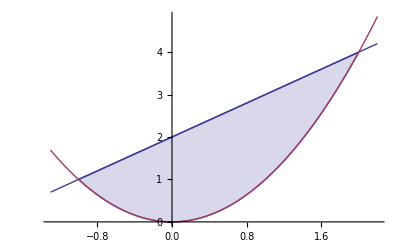

```mathematica
N[∫_-1^2 (f[x]-g[x])ⅆx]
p1:=Plot[{f[x],g[x]},{x,-1.3,2.2}]
p2:=Plot[{f[x],g[x]},{x,-1,2},Filling->{1->{2}}]
Show[p1,p2]
```

```mathematica
"c)"
f[x_]:=5x-x^2
g[x_]:=x
Solve[f[x]==g[x],x]
```

c)

{{x→0},{x→4}}

10.6667

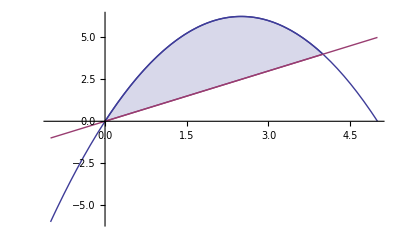

```mathematica
N[∫_0^4 (f[x]-g[x])ⅆx]
p1:=Plot[{f[x],g[x]},{x,-1,5}]
p2:=Plot[{f[x],g[x]},{x,0,4},Filling->{1->{2}}]
Show[p1,p2]
```

## Excedente del consumidor y del productor

a

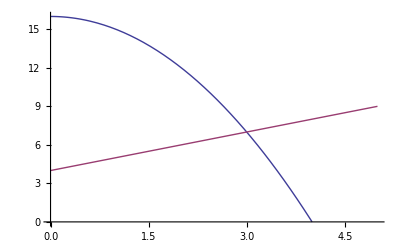

Cantidad de equilibrio:

{{q→-4},{q→3}}

Precio de equilibrio:

7

Superávit Consumidor:

18

Superávit Productor:

9/2

```mathematica
"a"
Dem[q_]:=16-q^2;Ofe[q_]:=4+q;
Plot[{Dem[q],Ofe[q]},{q,0,5},PlotRange->{0,16}]
"Cantidad de equilibrio:"
Solve[Ofe[q]==Dem[q],q]
"Precio de equilibrio:"
Dem[3]
"Superávit Consumidor:"
∫_0^3 (Dem[q]-Dem[3])ⅆq
"Superávit Productor:"
∫_0^3 (Ofe[3]-Ofe[q])ⅆq
```

## Integrales Impropias

```mathematica
"a)"
Limit[∫_1^a (1/x^3)ⅆx,a->∞]
```

a)

1/2

```mathematica
"b)"
Limit[∫_1^a x^(-3/2)ⅆx,a->∞]
```

b)

2

```mathematica
"c)"
Limit[∫_0^a ⅇ^-x ⅆx,a->∞]
```

c)

1